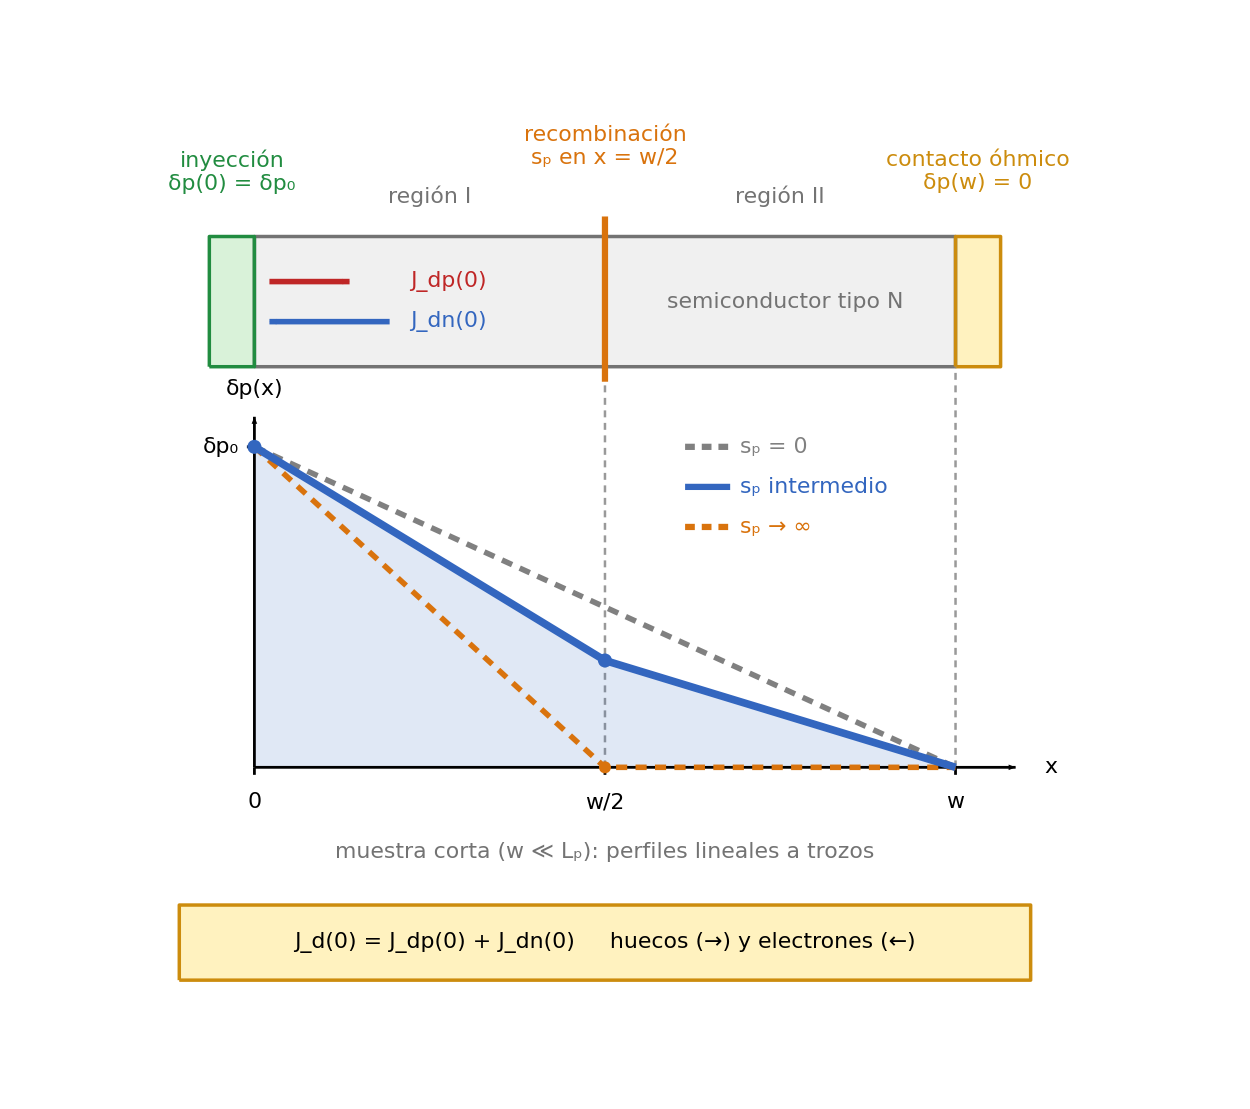

```mathematica
diagramaDifusionCorta = Module[
  {fs, beta, cAzulB, cRojo, cVerde, cVerdeF, cNar, cGris, cOro, cOroB,
   ox, W, y0, hs, yb0, yb1, pm, xs, ys, ins, insI, insD, caja, flecha,
   dp, dp0, curvaG, curva0, curvaI, items, leyenda},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;     (* tamaño de fuente único para todo el gráfico *)
  beta = 1.;   (* w s_p / (2 D_p) del caso intermedio: cualquier valor >= 0 *)
  cAzulB = RGBColor[0.20, 0.40, 0.75];  cRojo   = RGBColor[0.75, 0.15, 0.15];
  cVerde = RGBColor[0.13, 0.55, 0.25];  cVerdeF = RGBColor[0.85, 0.95, 0.85];
  cNar   = RGBColor[0.85, 0.45, 0.05];  cGris   = GrayLevel[0.45];
  cOro   = RGBColor[1.0, 0.95, 0.75];   cOroB   = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Geometría (x normalizada a w) ---------- *)
  {ox, W} = {4.0, 14.0};          (* origen y longitud de la barra *)
  {y0, hs} = {2.0, 6.4};          (* base y altura del perfil (valor de δp0) *)
  {yb0, yb1} = {10.0, 12.6};      (* límites verticales de la barra *)
  pm = 1/(2 + beta);              (* δp(w/2)/δp0 del caso intermedio *)
  xs[u_] := ox + W u;
  ys[v_] := y0 + hs v;

  (* perfiles, lineales a trozos: puntos en (x/w, δp/δp0) *)
  curvaG = {{xs[0], ys[1]}, {xs[0.5], ys[pm]}, {xs[1], ys[0]}};   (* s_p intermedio *)
  curva0 = {{xs[0], ys[1]}, {xs[1], ys[0]}};                      (* s_p = 0 *)
  curvaI = {{xs[0], ys[1]}, {xs[0.5], ys[0]}, {xs[1], ys[0]}};    (* s_p -> infinito *)

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  flecha[p1_, p2_, col_, s_: 0.016] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};
  dp[a_] := Row[{"δ", Style["p", Italic], "(", a, ")"}];
  dp0 = Subscript[Row[{"δ", Style["p", Italic]}], 0];

  (* leyenda de los tres casos *)
  items = {
    {GrayLevel[0.5], {7, 5}, Row[{Subscript["s", "p"], " = 0"}]},
    {cAzulB, {}, Row[{Subscript["s", "p"], " intermedio"}]},
    {cNar, {7, 5}, Row[{Subscript["s", "p"], " → ∞"}]}};
  leyenda = Table[
    {{items[[k, 1]], AbsoluteThickness[4.5], AbsoluteDashing[items[[k, 2]]],
      Line[{{ox + 8.6, 8.4 - 0.8 (k - 1)}, {ox + 9.5, 8.4 - 0.8 (k - 1)}}]},
     insI[items[[k, 3]], {ox + 9.7, 8.4 - 0.8 (k - 1)}, items[[k, 1]]]},
    {k, 3}];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* ===== Barra, contactos e interfaz ===== *)
    {GrayLevel[0.94], EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{ox, yb0}, {ox + W, yb1}]},
    {cVerdeF, EdgeForm[{AbsoluteThickness[2.5], cVerde}],
     Rectangle[{ox - 0.9, yb0}, {ox, yb1}]},
    {cOro, EdgeForm[{AbsoluteThickness[2.5], cOroB}],
     Rectangle[{ox + W, yb0}, {ox + W + 0.9, yb1}]},
    {cNar, AbsoluteThickness[4.5], Line[{{xs[0.5], yb0 - 0.3}, {xs[0.5], yb1 + 0.4}}]},

    (* etiquetas de la barra *)
    ins["región I", {ox + 3.5, 13.4}, cGris],
    ins["región II", {ox + 10.5, 13.4}, cGris],
    ins[Column[{"recombinación",
       Row[{Subscript["s", "p"], " en ", Style["x", Italic], " = ", Style["w", Italic], "/2"}]},
      Center], {xs[0.5], 14.4}, cNar],
    ins[Column[{"inyección", Row[{dp[0], " = ", dp0}]}, Center], {ox - 0.45, 13.9}, cVerde],
    ins[Column[{"contacto óhmico", Row[{dp[Style["w", Italic]], " = 0"}]}, Center],
     {ox + W + 0.45, 13.9}, cOroB],
    ins["semiconductor tipo N", {ox + 10.6, 11.3}, cGris],

    (* corrientes de difusión en x = 0 *)
    flecha[{ox + 0.3, 11.7}, {ox + 1.9, 11.7}, cRojo],
    insI[Row[{Subscript["J", "dp"], "(0)"}], {ox + 3.1, 11.7}, cRojo],
    flecha[{ox + 2.7, 10.9}, {ox + 0.3, 10.9}, cAzulB],
    insI[Row[{Subscript["J", "dn"], "(0)"}], {ox + 3.1, 10.9}, cAzulB],

    (* guías verticales hacia el perfil *)
    {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{5, 4}],
     Line[{{xs[0.5], y0}, {xs[0.5], yb0 - 0.3}}], Line[{{xs[1], y0}, {xs[1], yb0}}]},

    (* ===== Perfil de portadores ===== *)
    {Opacity[0.15, cAzulB], EdgeForm[None], Polygon[Append[curvaG, {xs[0], ys[0]}]]},
    {Black, AbsoluteThickness[2], Arrowheads[0.016],
     Arrow[{{ox, y0}, {ox + W + 1.2, y0}}], Arrow[{{ox, y0}, {ox, 9.0}}]},
    ins[Style["x", Italic], {ox + W + 1.9, y0}],
    ins[dp[Style["x", Italic]], {ox, 9.55}],
    {Black, AbsoluteThickness[2], Line[{{ox - 0.15, ys[1]}, {ox, ys[1]}}]},
    insD[dp0, {ox - 0.3, ys[1]}],

    (* marcas del eje x *)
    Table[{Black, AbsoluteThickness[2], Line[{{xs[u], y0}, {xs[u], y0 - 0.15}}]},
     {u, {0, 0.5, 1}}],
    ins["0", {xs[0], y0 - 0.7}],
    ins[Row[{Style["w", Italic], "/2"}], {xs[0.5], y0 - 0.7}],
    ins[Style["w", Italic], {xs[1], y0 - 0.7}],

    (* curvas: s_p = 0, s_p -> infinito y caso intermedio *)
    {GrayLevel[0.5], AbsoluteThickness[4], AbsoluteDashing[{8, 6}], Line[curva0]},
    {cNar, AbsoluteThickness[4], AbsoluteDashing[{8, 6}], Line[curvaI]},
    {cAzulB, AbsoluteThickness[5.5], Line[curvaG]},
    {cAzulB, Disk[{xs[0], ys[1]}, 0.14], Disk[{xs[0.5], ys[pm]}, 0.14]},
    {cNar, Disk[{xs[0.5], ys[0]}, 0.12]},
    leyenda,

    (* ===== Notas ===== *)
    ins[Row[{"muestra corta (", Style["w", Italic], " ≪ ",
       Subscript["L", "p"], "): perfiles lineales a trozos"}],
     {ox + 7, 0.3}, cGris],
    caja[{ox + 7, -1.5}, {17, 1.5}, cOro, cOroB],
    ins[Row[{Subscript["J", "d"], "(0) = ", Subscript["J", "dp"], "(0) + ",
       Subscript["J", "dn"], "(0)     huecos (→) y electrones (←)"}],
     {ox + 7, -1.5}]
   },
   ImageSize -> 1250,
   PlotRange -> {{1.2, 21.6}, {-2.8, 15.3}},
   PlotRangePadding -> None,
   AspectRatio -> 18.1/20.4,
   Background -> White]
];
diagramaDifusionCorta
```